# Circuit 1

## Module

```mathematica
(*Gates*)
Rx[θ_]:={{Cos[θ/2],-I Sin[θ/2]},{-I Sin[θ/2],Cos[θ/2]}}
Ry[θ_]:={{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}}
Rz[θ_]:={{Exp[-I θ/2],0},{0,Exp[I θ/2]}}
(*Tensor calculation*)
TwoQubit[mat1_,mat2_]:=TensorProduct[mat1,mat2]//ArrayFlatten
FourQubit[{mat1_,mat2_,mat3_,mat4_}]:=TensorProduct[TwoQubit[mat1,mat2],TwoQubit[mat3,mat4]]//ArrayFlatten
```

```mathematica
(*Parameter condition*)
condition={θ[1]∈Reals,θ[1]≥0,θ[2]∈Reals,θ[2]≥0,θ[3]∈Reals,θ[3]≥0,θ[4]∈Reals,θ[4]≥0,θ[5]∈Reals,θ[5]≥0,θ[6]∈Reals,θ[6]≥0,θ[7]∈Reals,θ[7]≥0,θ[8]∈Reals,θ[8]≥0,1≥x≥0,1≥y≥0,x∈Reals,y∈Reals}
```

{θ[1]∈ℝ,θ[1]≥0,θ[2]∈ℝ,θ[2]≥0,θ[3]∈ℝ,θ[3]≥0,θ[4]∈ℝ,θ[4]≥0,θ[5]∈ℝ,θ[5]≥0,θ[6]∈ℝ,θ[6]≥0,θ[7]∈ℝ,θ[7]≥0,θ[8]∈ℝ,θ[8]≥0,1≥x≥0,1≥y≥0,x∈ℝ,y∈ℝ}

```mathematica
(*input state |0000>*)
input=Flatten[FourQubit[{{0,1},{0,1},{0,1},{0,1}}]];
(*Embedding Circuit*)
Embeding=Assuming[condition,FourQubit[Table[Rz[Pi/4],{i,1,4}]].FourQubit[Table[Ry[Pi/4],{i,1,4}]].FourQubit[{Rx[x],Rx[y],Rx[x],Rx[y]}]//Simplify];
(*Example Circuit 1*)
circuit1=Assuming[condition,FourQubit[Table[Rz[θ[i+4]],{i,1,4}]].FourQubit[Table[Rx[θ[i]],{i,1,4}]]];
```

```mathematica
(*result state*)
result=circuit1.Embeding.input;
(*Print First element*)
%[[1]]/.{x->0,y->0} //Simplify
```

1/8 ⅇ^(-1/2 ⅈ (θ[5]+θ[6]+θ[7]+θ[8])) (Sin[θ[1]/2] (-Sin[θ[2]/2] (Cos[θ[3]/2]-(2-2 ⅈ) Cos[π/8]^2 Sin[θ[3]/2]) (Cos[θ[4]/2]-(2-2 ⅈ) Cos[π/8]^2 Sin[θ[4]/2])+Cos[θ[2]/2] (Cos[θ[3]/2] ((2+2 ⅈ) Cos[θ[4]/2] Sin[π/8]^2-Sin[θ[4]/2])-Sin[θ[3]/2] (Cos[θ[4]/2]-(2-2 ⅈ) Cos[π/8]^2 Sin[θ[4]/2])))+Cos[θ[1]/2] (-Cos[θ[2]/2] ((2+2 ⅈ) Cos[θ[3]/2] Sin[π/8]^2-Sin[θ[3]/2]) ((2+2 ⅈ) Cos[θ[4]/2] Sin[π/8]^2-Sin[θ[4]/2])+Sin[θ[2]/2] (Cos[θ[3]/2] ((2+2 ⅈ) Cos[θ[4]/2] Sin[π/8]^2-Sin[θ[4]/2])-Sin[θ[3]/2] (Cos[θ[4]/2]-(2-2 ⅈ) Cos[π/8]^2 Sin[θ[4]/2]))))

## Test

```mathematica
(*Test Norm is equal to 1*)
Norm[result/.Table[θ[i]->1,{i,1,8}]/.{x->1,y->1}//N]
```

1.

```mathematica
(*Probability amplitute for each base*)
ProbAmp1=Table[Norm[(result[[j]]/.Table[θ[i]->0,{i,1,8}]/.{x->1,y->1})//N],{j,1,16}];
(*Sum of Prob square eqaul to 1*)
Total[ProbAmp1^2]
```

1.

```mathematica
(*param1={1,0,0,0,0,0,0,0};*)
fundata[param1_]:=fun[param1]=
Module[{param,data1,ProbAmp,max,loc,conv},
Do[
param=Table[θ[i]->param1[[i]],{i,1,8}];
data1={x->0.5*Pi*x1,y->0.5*Pi*y1};
ProbAmp=Table[Norm[(result[[j]]/.param/.data1)],{j,1,16}];
max=Max[ProbAmp];
loc=Position[ProbAmp,max][[1,1]];
conv[x1,y1]=If[MemberQ[{1,2,3,4,13,14,15,16},loc],0,1];
,{x1,0,1,0.05},{y1,0,1,0.05}];
Flatten[Table[{x1,y1,conv[x1,y1]},{x1,0,1,0.05},{y1,0,1,0.05}],1]
]
```

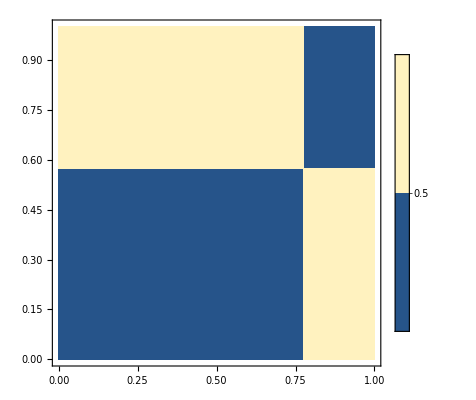

```mathematica
ListContourPlot[fundata[{0.45662733,0.99454071,0.81372455,0.45451458,0.40753335,0.1246864,-0.27016841,2.85858817}],PlotLegends->Automatic,Contours->1,InterpolationOrder->0]
```

```mathematica
Clear[fun]
(*param1={1,0,0,0,0,0,0,0};*)
fun[param1_]:=fun[param1]=
Module[{param,data1,ProbAmp,max,loc,conv,dat},
Do[
param=Table[θ[i]->param1[[i]],{i,1,8}];
data1={x->x1,y->y1};
ProbAmp=Table[Norm[(result[[j]]/.param/.data1)],{j,1,16}];
max=Max[ProbAmp];
loc=Position[ProbAmp,max][[1,1]];
conv[x1,y1]=If[MemberQ[{1,2,3,4,13,14,15,16},loc],0,1];
,{x1,0,1,0.2},{y1,0,1,0.2}];
dat=Table[conv[x1,y1],{x1,0,1,0.2},{y1,0,1,0.2}];
ArrayPlot[Transpose[dat]]
]
```

## Plot

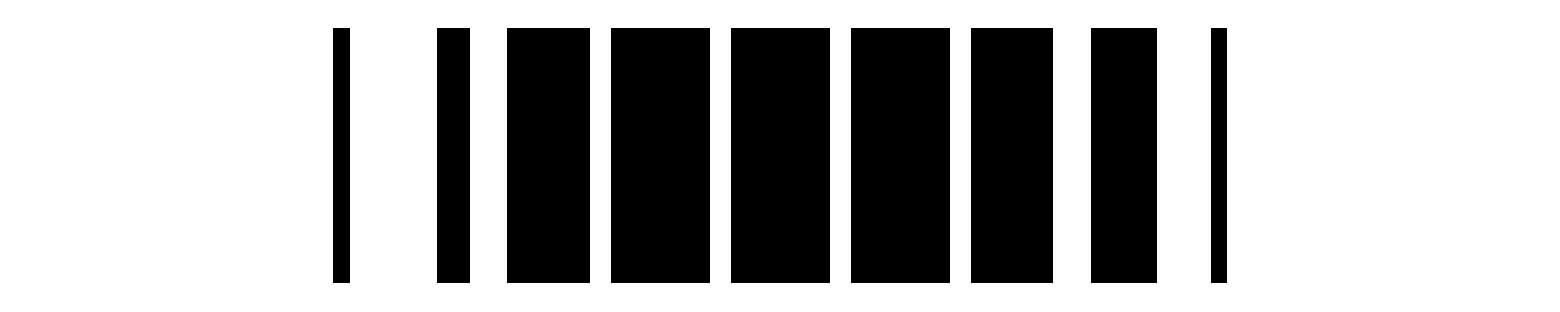

```mathematica
TableForm[Table[fun[{i,0,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

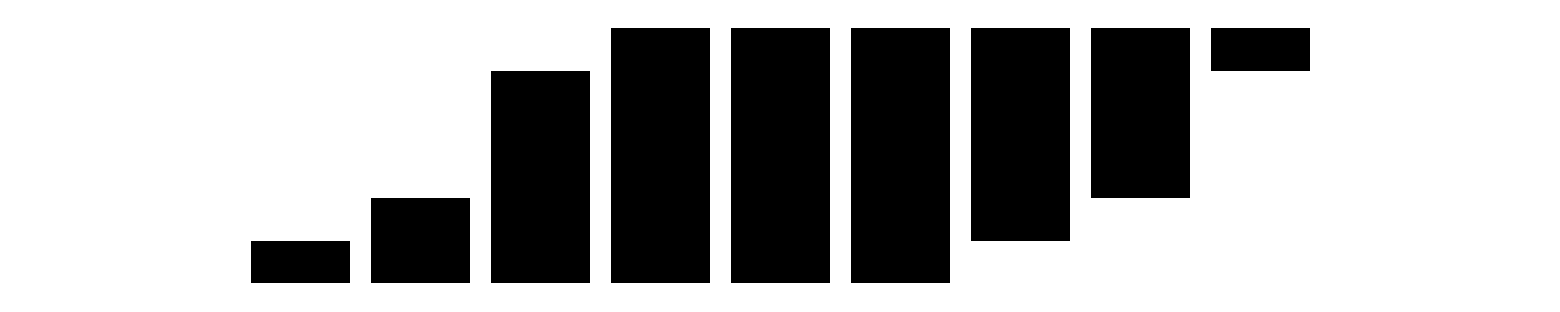

```mathematica
TableForm[Table[fun[{0,i,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

```mathematica
TableForm[Table[fun[{0,0,i,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

-Graphics-

```mathematica
TableForm[Table[fun[{0,0,0,i,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

-Graphics-

```mathematica
TableForm[Table[fun[{0,0,0,0,i,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

-Graphics-

```mathematica
TableForm[Table[fun[{i,j,0,0,0,0,0,0}],{i,0,2Pi,Pi/6},{j,0,2Pi,Pi/6}]]
```

-Graphics-

```mathematica
TableForm[Table[fun[{0,i,j,0,0,0,0,0}],{i,0,2Pi,Pi/6},{j,0,2Pi,Pi/6}]]
```

-Graphics-

```mathematica
TableForm[Table[fun[{0,0,i,j,0,0,0,0}],{i,0,2Pi,Pi/6},{j,0,2Pi,Pi/6}]]
```

-Graphics-

```mathematica
TableForm[Table[fun[{0,0,0,i,j,0,0,0}],{i,0,2Pi,Pi/6},{j,0,2Pi,Pi/6}]]
```

-Graphics-

```mathematica
TableForm[Table[fun[{1,1,1,i,j,0,0,0}],{i,0,2Pi,Pi/6},{j,0,2Pi,Pi/6}]]
```

-Graphics-

```mathematica
TableForm[Table[fun[{0,1,i,j,0,0,0,0}],{i,0,2Pi,Pi/6},{j,0,2Pi,Pi/6}]]
```

-Graphics-

```mathematica
TableForm[Table[fun[{2,1,i,j,0,0,0,0}],{i,0,2Pi,Pi/6},{j,0,2Pi,Pi/6}]]
```

-Graphics-

# Circuit 2

## Module

```mathematica
(*Gates*)
Rx[θ_]:={{Cos[θ/2],-I Sin[θ/2]},{-I Sin[θ/2],Cos[θ/2]}}
Ry[θ_]:={{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}}
Rz[θ_]:={{Exp[-I θ/2],0},{0,Exp[I θ/2]}}
Cnot={{0,1,0,0},{1,0,0,0},{0,0,1,0},{0,0,0,1}};
(*Tensor calculation*)
TwoQubit[mat1_,mat2_]:=TensorProduct[mat1,mat2]//ArrayFlatten
FourQubit[{mat1_,mat2_,mat3_,mat4_}]:=TensorProduct[TwoQubit[mat1,mat2],TwoQubit[mat3,mat4]]//ArrayFlatten
```

```mathematica
(*Parameter condition*)
condition={θ[1]∈Reals,θ[1]≥0,θ[2]∈Reals,θ[2]≥0,θ[3]∈Reals,θ[3]≥0,θ[4]∈Reals,θ[4]≥0,θ[5]∈Reals,θ[5]≥0,θ[6]∈Reals,θ[6]≥0,θ[7]∈Reals,θ[7]≥0,θ[8]∈Reals,θ[8]≥0,1≥x≥0,1≥y≥0,x∈Reals,y∈Reals}
```

{θ[1]∈ℝ,θ[1]≥0,θ[2]∈ℝ,θ[2]≥0,θ[3]∈ℝ,θ[3]≥0,θ[4]∈ℝ,θ[4]≥0,θ[5]∈ℝ,θ[5]≥0,θ[6]∈ℝ,θ[6]≥0,θ[7]∈ℝ,θ[7]≥0,θ[8]∈ℝ,θ[8]≥0,1≥x≥0,1≥y≥0,x∈ℝ,y∈ℝ}

```mathematica
ide={{1,0},{0,1}};
xG={{0,1},{1,0}};
```

```mathematica
cnot1=FourQubit[{ide,ide,ide,{{1,0},{0,0}}}]+FourQubit[{ide,ide,xG,{{0,0},{0,1}}}]
cnot2=FourQubit[{ide,ide,{{1,0},{0,0}},ide}]+FourQubit[{ide,xG,{{0,0},{0,1}},ide}]
cnot3=FourQubit[{ide,{{1,0},{0,0}},ide,ide}]+FourQubit[{xG,{{0,0},{0,1}},ide,ide}]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0}}

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0}}

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0}}

```mathematica
(*input state |0000>*)
input=Flatten[FourQubit[{{0,1},{0,1},{0,1},{0,1}}]];
(*Embedding Circuit*)
Embeding=Assuming[condition,FourQubit[Table[Rz[Pi/4],{i,1,4}]].FourQubit[Table[Ry[Pi/4],{i,1,4}]].FourQubit[{Rx[x],Rx[y],Rx[x],Rx[y]}]//Simplify];
(*Example Circuit 1*)
circuit2=Assuming[condition,cnot3.cnot2.cnot1.FourQubit[Table[Rz[θ[i+4]],{i,1,4}]].FourQubit[Table[Rx[θ[i]],{i,1,4}]]];
```

```mathematica
(*result state*)
result=circuit2.Embeding.input;
```

## Test

```mathematica
(*Test Norm is equal to 1*)
Norm[result/.Table[θ[i]->1,{i,1,8}]/.{x->1,y->1}//N]
```

1.

```mathematica
Clear[fun]
(*param1={1,0,0,0,0,0,0,0};*)
fun[param1_]:=fun[param1]=
Module[{param,data1,ProbAmp,max,loc,conv,dat},
Do[
param=Table[θ[i]->param1[[i]],{i,1,8}];
data1={x->x1,y->y1};
ProbAmp=Table[Norm[(result[[j]]/.param/.data1)],{j,1,16}];
max=Max[ProbAmp];
loc=Position[ProbAmp,max][[1,1]];
conv[x1,y1]=If[MemberQ[{1,2,3,4,13,14,15,16},loc],0,1];
,{x1,0,1,0.2},{y1,0,1,0.2}];
dat=Table[conv[x1,y1],{x1,0,1,0.2},{y1,0,1,0.2}];
ArrayPlot[Transpose[dat]]
]
```

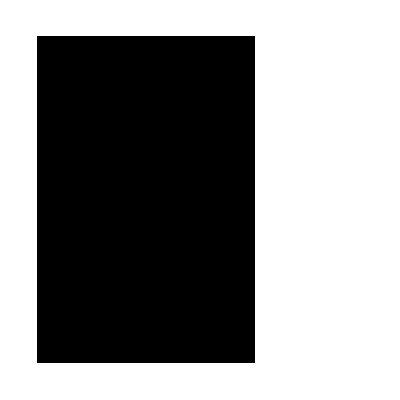

```mathematica
fun[{1.45032936,0,1.80742658,1.28699465,1.24001342,1.11838843,.723533625,2.02610810}]
```

## Plot

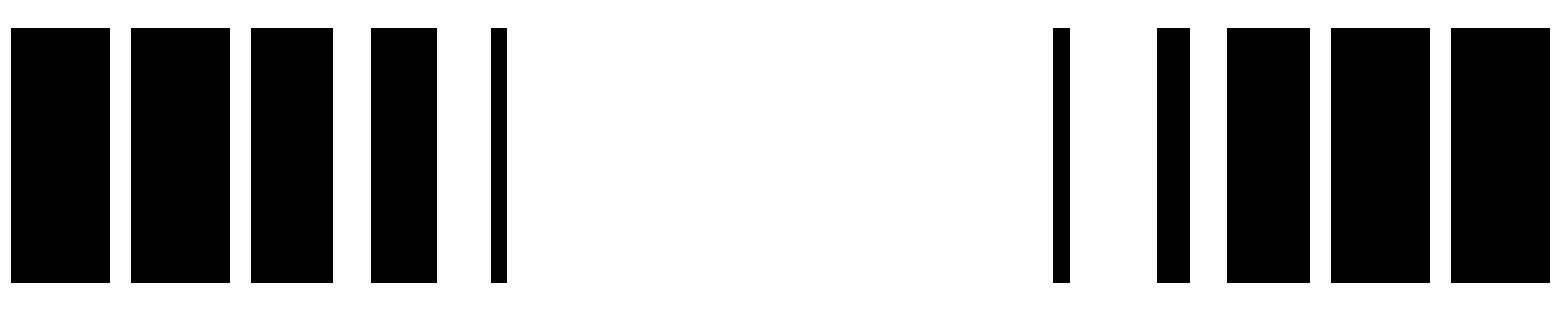

```mathematica
TableForm[Table[fun[{i,0,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

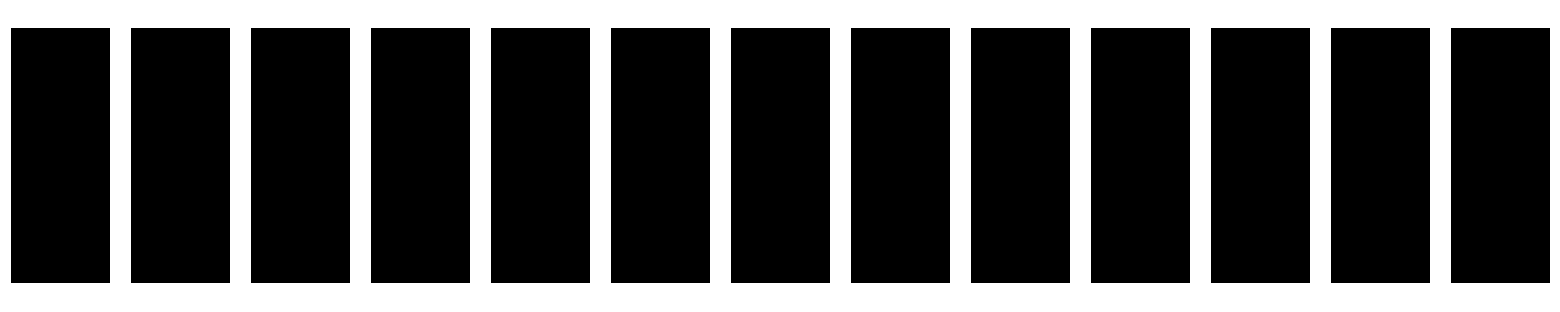

```mathematica
TableForm[Table[fun[{0,i,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

```mathematica
TableForm[Table[fun[{0,0,i,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

-Graphics-

```mathematica
TableForm[Table[fun[{0,0,0,i,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

-Graphics-

```mathematica
TableForm[Table[fun[{0,0,0,0,i,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

-Graphics-

```mathematica
TableForm[Table[fun[{i,j,0,0,0,0,0,0}],{i,0,2Pi,Pi/6},{j,0,2Pi,Pi/6}]]
```

$Aborted

```mathematica
TableForm[Table[fun[{0,i,j,0,0,0,0,0}],{i,0,2Pi,Pi/6},{j,0,2Pi,Pi/6}]]
```

-Graphics-

```mathematica
TableForm[Table[fun[{0,0,i,j,0,0,0,0}],{i,0,2Pi,Pi/6},{j,0,2Pi,Pi/6}]]
```

-Graphics-

```mathematica
TableForm[Table[fun[{0,0,0,i,j,0,0,0}],{i,0,2Pi,Pi/6},{j,0,2Pi,Pi/6}]]
```

-Graphics-

```mathematica
TableForm[Table[fun[{1,1,1,i,j,0,0,0}],{i,0,2Pi,Pi/6},{j,0,2Pi,Pi/6}]]
```

-Graphics-

```mathematica
TableForm[Table[fun[{0,1,i,j,0,0,0,0}],{i,0,2Pi,Pi/6},{j,0,2Pi,Pi/6}]]
```

-Graphics-

```mathematica
TableForm[Table[fun[{2,1,i,j,0,0,0,0}],{i,0,2Pi,Pi/6},{j,0,2Pi,Pi/6}]]
```

-Graphics-

# Circuit 19

## Module

```mathematica
ide={{1,0},{0,1}};
xG={{0,1},{1,0}};
```

```mathematica
(*Gates*)
Rx[θ_]:={{Cos[θ/2],-I Sin[θ/2]},{-I Sin[θ/2],Cos[θ/2]}}
Ry[θ_]:={{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}}
Rz[θ_]:={{Exp[-I θ/2],0},{0,Exp[I θ/2]}}
(*Tensor calculation*)
TwoQubit[mat1_,mat2_]:=TensorProduct[mat1,mat2]//ArrayFlatten
FourQubit[{mat1_,mat2_,mat3_,mat4_}]:=TensorProduct[TwoQubit[mat1,mat2],TwoQubit[mat3,mat4]]//ArrayFlatten
```

```mathematica
cRx1[θ_]:=FourQubit[{ide,ide,ide,{{1,0},{0,0}}}]+FourQubit[{Rx[θ],ide,ide,{{0,0},{0,1}}}]
cRx2[θ_]:=FourQubit[{ide,ide,{{1,0},{0,0}},ide}]+FourQubit[{ide,ide,{{0,0},{0,1}},Rx[θ]}]
cRx3[θ_]:=FourQubit[{ide,{{1,0},{0,0}},ide,ide}]+FourQubit[{ide,{{0,0},{0,1}},Rx[θ],ide}]
cRx4[θ_]:=FourQubit[{{{1,0},{0,0}},ide,ide,ide}]+FourQubit[{{{0,0},{0,1}},Rx[θ],ide,ide}]
```

```mathematica
(*Parameter condition*)
condition={θ[1]∈Reals,θ[1]≥0,θ[2]∈Reals,θ[2]≥0,θ[3]∈Reals,θ[3]≥0,θ[4]∈Reals,θ[4]≥0,θ[5]∈Reals,θ[5]≥0,θ[6]∈Reals,θ[6]≥0,θ[7]∈Reals,θ[7]≥0,θ[8]∈Reals,θ[8]≥0,1≥x≥0,1≥y≥0,x∈Reals,y∈Reals}
```

{θ[1]∈ℝ,θ[1]≥0,θ[2]∈ℝ,θ[2]≥0,θ[3]∈ℝ,θ[3]≥0,θ[4]∈ℝ,θ[4]≥0,θ[5]∈ℝ,θ[5]≥0,θ[6]∈ℝ,θ[6]≥0,θ[7]∈ℝ,θ[7]≥0,θ[8]∈ℝ,θ[8]≥0,1≥x≥0,1≥y≥0,x∈ℝ,y∈ℝ}

```mathematica
(*input state |0000>*)
input=Flatten[FourQubit[{{0,1},{0,1},{0,1},{0,1}}]];
(*Embedding Circuit*)
Embeding=Assuming[condition,FourQubit[Table[Rz[Pi/4],{i,1,4}]].FourQubit[Table[Ry[Pi/4],{i,1,4}]].FourQubit[{Rx[x],Rx[y],Rx[x],Rx[y]}]//Simplify];
(*Example Circuit 1*)
circuit19=Assuming[condition,
cRx4[θ[20]].cRx3[θ[19]].cRx2[θ[18]].cRx1[θ[17]].FourQubit[Table[Rz[θ[i+16]],{i,1,4}]].FourQubit[Table[Rx[θ[i+12]],{i,1,4}]].cRx4[θ[12]].cRx3[θ[11]].cRx2[θ[10]].cRx1[θ[9]].FourQubit[Table[Rz[θ[i+4]],{i,1,4}]].FourQubit[Table[Rx[θ[i]],{i,1,4}]]
];
```

```mathematica
(*result state*)
result=circuit19.Embeding.input;
```

## Test

```mathematica
(*Test Norm is equal to 1*)
Norm[result/.Table[θ[i]->1,{i,1,20}]/.{x->1,y->1}//N]
```

1.

```mathematica
Clear[fun]
(*param1={1,0,0,0,0,0,0,0};*)
fun[param1_]:=fun[param1]=
Module[{param,data1,ProbAmp,max,loc,conv,dat},
Do[
param=Table[θ[i]->param1[[i]],{i,1,20}];
data1={x->x1,y->y1};
ProbAmp=Table[Norm[(result[[j]]/.param/.data1)],{j,1,16}];
max=Max[ProbAmp];
loc=Position[ProbAmp,max][[1,1]];
conv[x1,y1]=If[MemberQ[{1,2,3,4,13,14,15,16},loc],0,1];
,{x1,0,1,0.1},{y1,0,1,0.1}];
dat=Table[conv[x1,y1],{x1,0,1,0.1},{y1,0,1,0.1}];
ArrayPlot[Transpose[dat]]
]
```

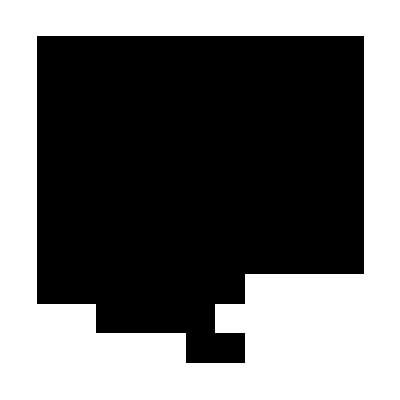

```mathematica
fun[{1.36971838,0.08144966,1.7268156,1.36760563,1.3206244,1.03777745,0.64292265,1.94549712,0.94139292,0.83826261,1.95134949,1.66234892,0.42279537,1.61345325,0.57943493,2.46720313,2.68284251,1.55269082,2.65955134,0.25021365}]
```

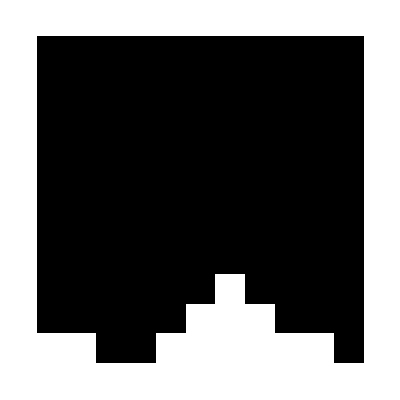

```mathematica
fun[{1.61602151,-0.16485347,1.97311873,1.1213025,1.07432127,1.28408058,0.88922578,2.19180025,0.69508979,0.59195948,2.19765262,1.41604579,0.17649224,1.85975638,0.3331318,2.71350626,2.92914564,1.79899395,2.90585447,0.00391051,1.83358054,0.45140673,1.59128909,0.05695768,0.64578796,2.12103381,0.95634077,0.08967665,0.44580923,1.34531482,1.71590086,0.38749191,1.76559393,1.76391178,1.34094484,0.96915598,2.24698247,2.06844,0.75617922,2.44778155}]
```

```mathematica
fun[{0.8227458,0.10109647,1.14856896,0.91988879,0.88997961,0.70991365,0.45854127,1.18929793,0.64855335,0.48441055,1.19302366,1.00904018,0.21991589,1.07640025,0.31963573,1.52142629,1.65870658,1.03771768,1.64387897,0.11004695,0.96124818,0.08132901,0.80700065,0.24230583,0.20507594,1.24273462,0.501268,0.16464736,0.39136841,0.65040857,0.88633097,0.35424245,1.33005745,1.01538367,0.96122944,0.7245413,1.63651891,1.20925236,0.3738412,1.4507487}]
```

-Graphics-

```mathematica
%[[1]]
```

Raster[{{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1}},{{0,0},{11,11}},{0,1}]

```mathematica
TableForm[Table[fun[{i,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

-Graphics-

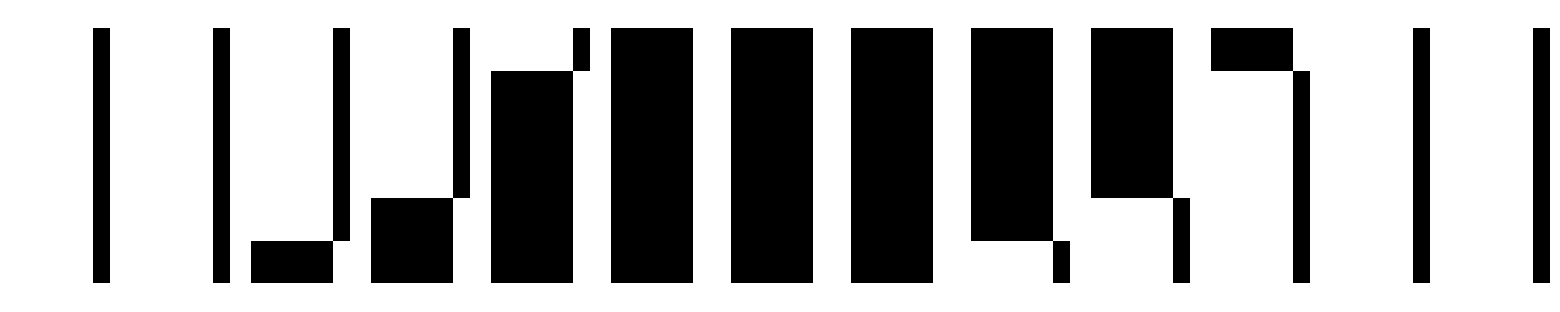

```mathematica
TableForm[Table[fun[{1,i,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

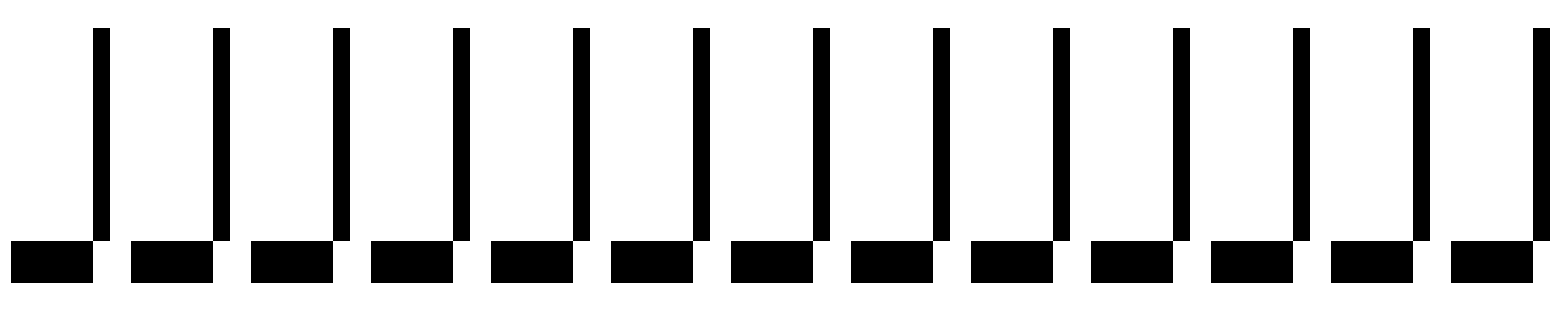

```mathematica
TableForm[Table[fun[{1,1,i,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

```mathematica
TableForm[Table[fun[{1,1,1,i,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

-Graphics-

```mathematica
TableForm[Table[fun[{1,1,1,1,i,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

-Graphics-

```mathematica
TableForm[Table[fun[{1,1,1,1,1,i,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

-Graphics-

```mathematica
TableForm[Table[fun[{1,1,1,1,1,1,i,0,0,0,0,0,0,0,0,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

-Graphics-

```mathematica
TableForm[Table[fun[{1,1,1,1,1,1,1,i,0,0,0,0,0,0,0,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

-Graphics-

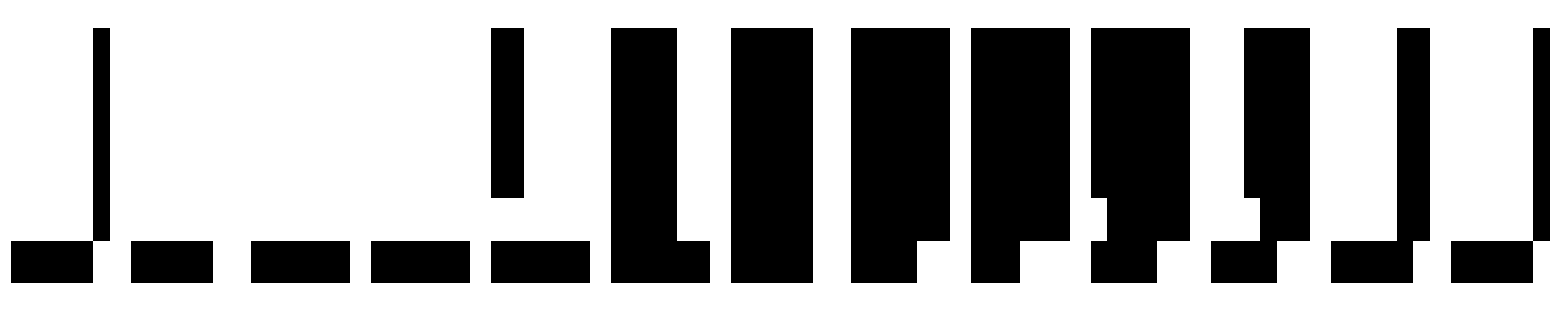

```mathematica
TableForm[Table[fun[{1,1,1,1,1,1,1,1,i,0,0,0,0,0,0,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

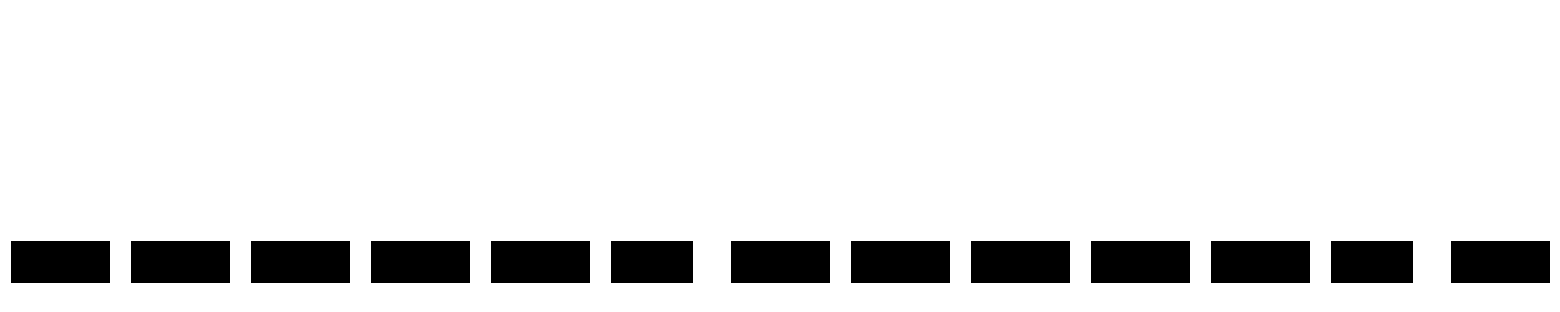

```mathematica
TableForm[Table[fun[{1,1,1,1,1,1,1,1,1,i,0,0,0,0,0,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

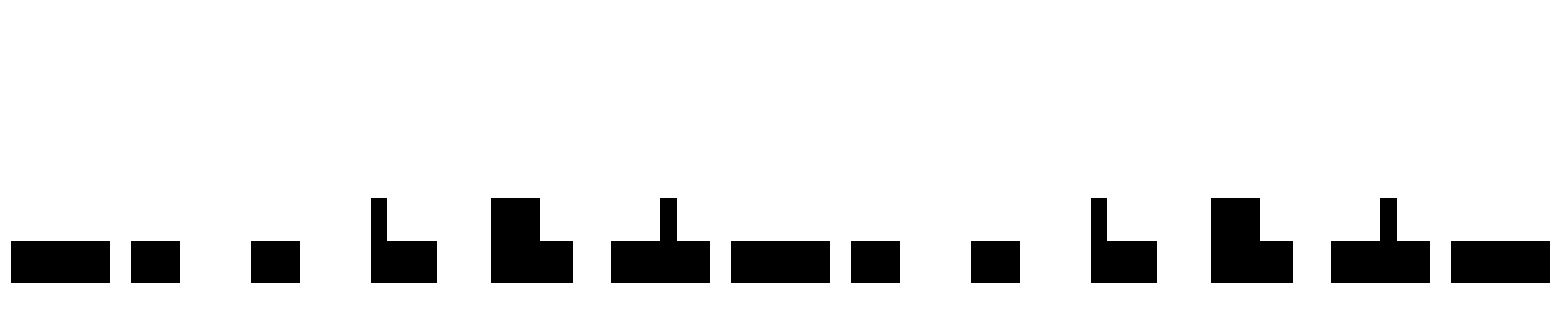

```mathematica
TableForm[Table[fun[{1,1,1,1,1,1,1,1,1,1,i,0,0,0,0,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

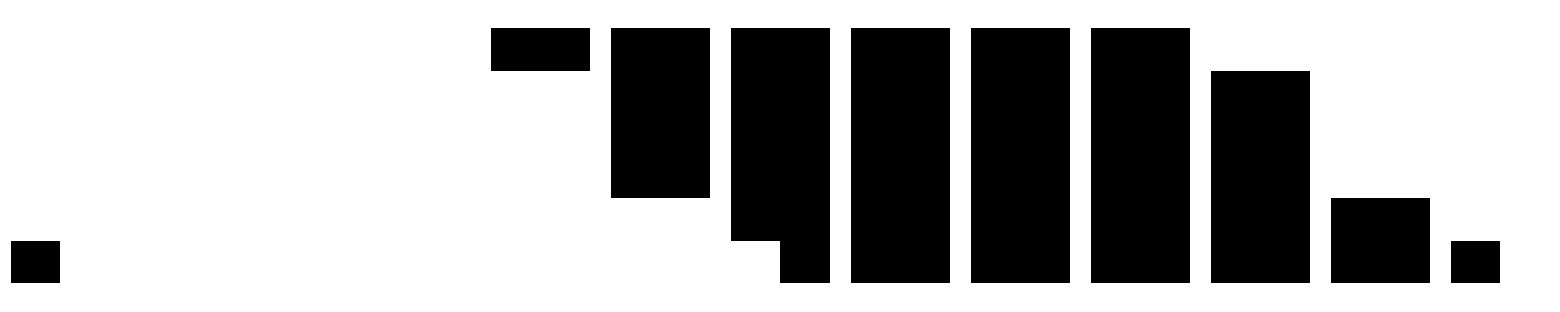

```mathematica
TableForm[Table[fun[{1,1,1,1,1,1,1,1,1,1,1,i,0,0,0,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

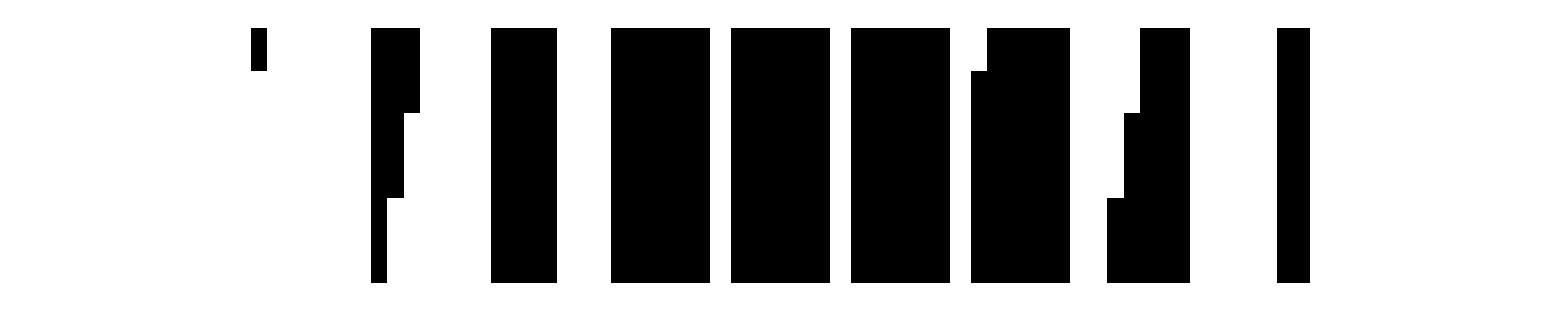

```mathematica
TableForm[Table[fun[{1,1,1,1,1,1,1,1,1,1,1,1,i,0,0,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

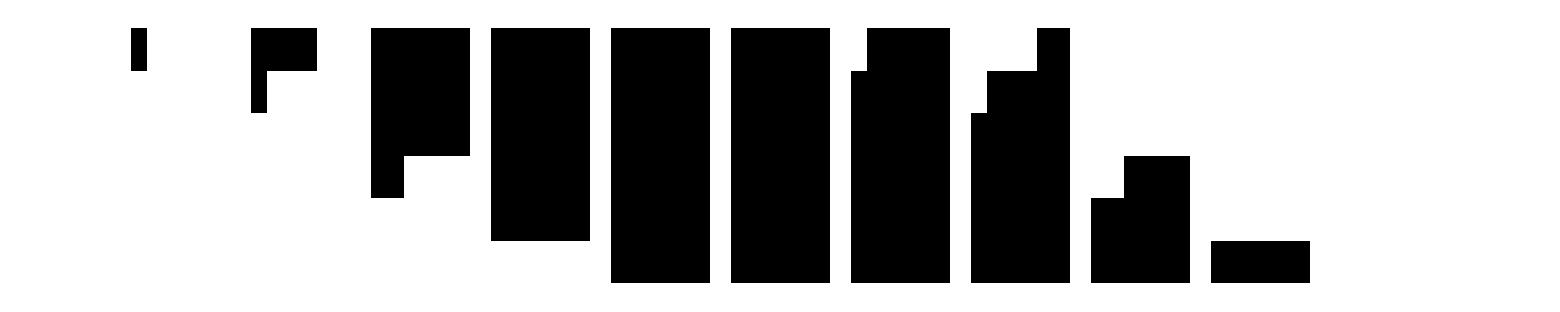

```mathematica
TableForm[Table[fun[{1,1,1,1,1,1,1,1,1,1,1,1,1,i,0,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

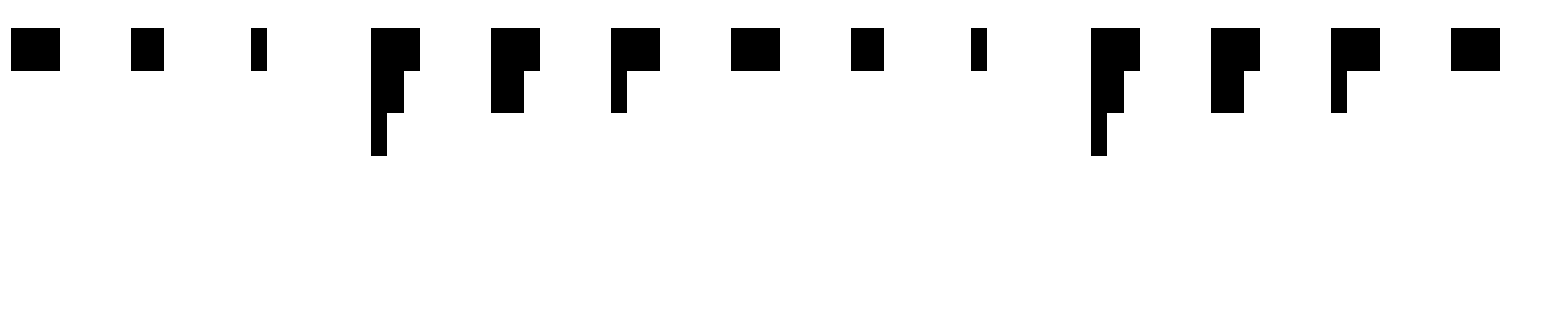

```mathematica
TableForm[Table[fun[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,i,0,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

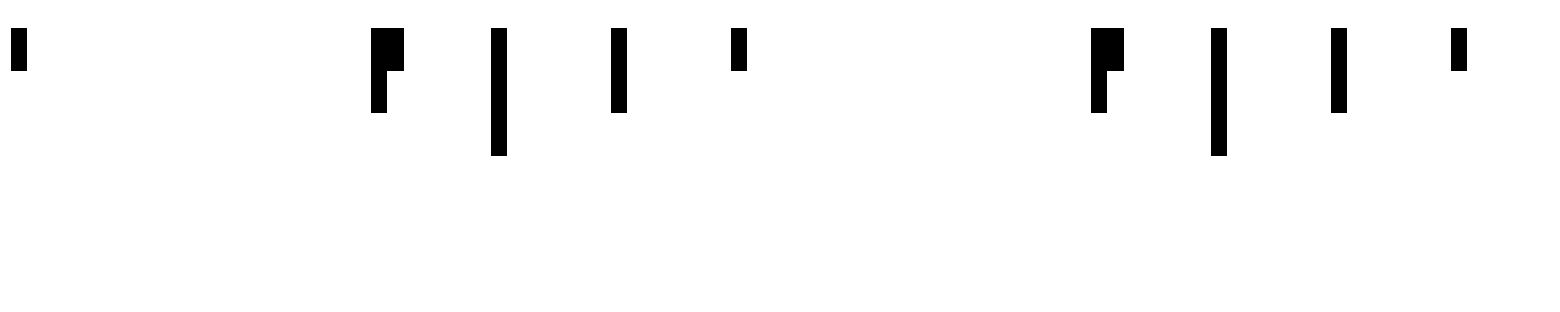

```mathematica
TableForm[Table[fun[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,i,0,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

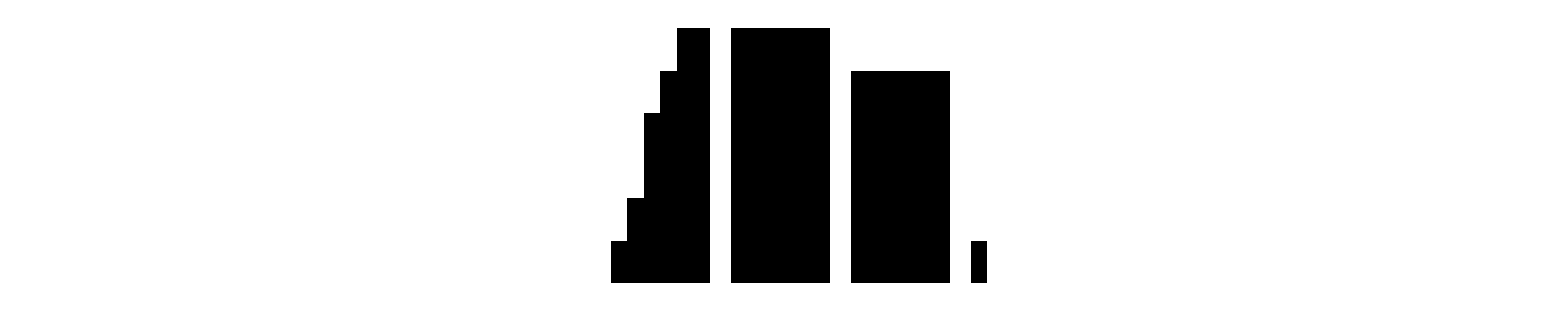

```mathematica
TableForm[Table[fun[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,i,0,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

```mathematica
TableForm[Table[fun[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,i,0,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

-Graphics-

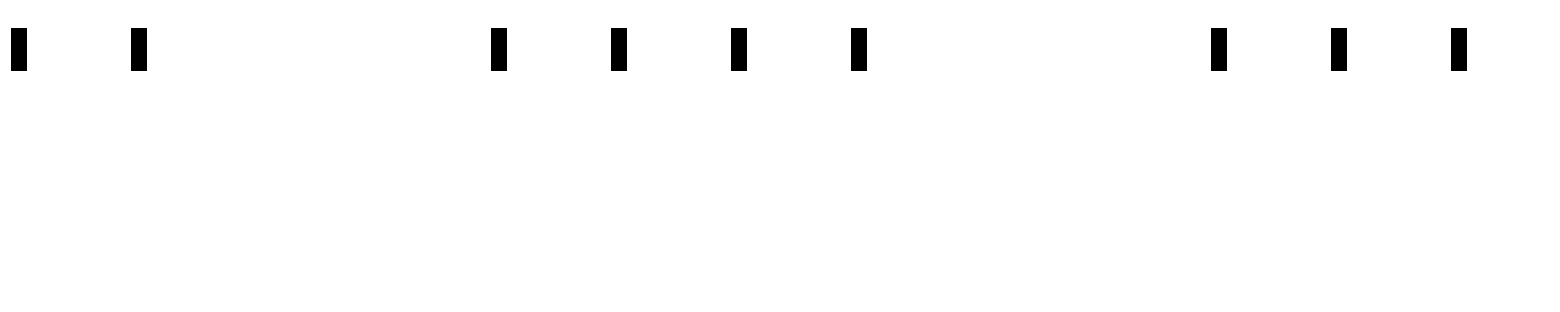

```mathematica
TableForm[Table[fun[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,i,0,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

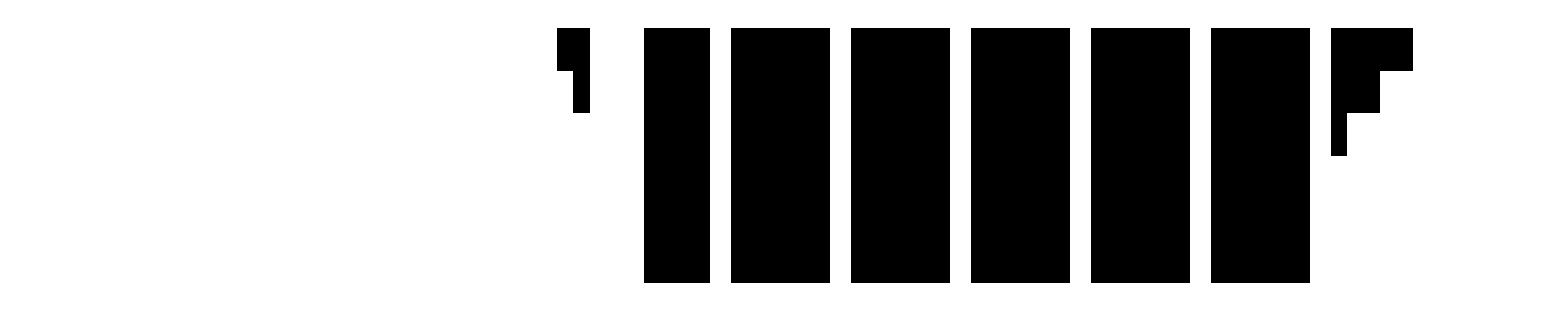

```mathematica
TableForm[Table[fun[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,i,0}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```

```mathematica
TableForm[Table[fun[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,i}],{i,0,2Pi,Pi/6}],TableDirections->Row]
```